### From 2016’s Final Exam

1. D.C. Voltage Regulator (50 pts, Recommended time: 40 mins): Consider the reverse bias I-V characteristics of a Zener diode shown below (dotted line). We want to use a piecewise linear model for the Zener diode under reverse bias condition to analyze its I-V behavior.  In this piecewise linear model,

Id(Vd) = Piecewise[{{0, -Vzo<Vd<0  (Off state)}, {1/r_z·(Vd-(-Vzo)), Vd ≤ -Vzo        (REVERSE ON state)}}] 

The Id(Vd) for this piecewise linear model is shown in the solid line. The small signal resistance r_z, defined as ( (∂ Id)/(∂ Vd))^-1 is 100Ω for –20mA < Id < –5mA.

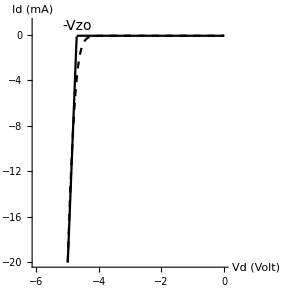

(a) When biased at Vz = –5V, the Zener diode shows a current Id of –15 mA. Find the value for Vzo. (Vzo is a positive quantity) (5 pts)

(b) Find Vd when Id = –5mA according to the piecewise linear model. (5 pts)

The Zener diode is used to build a voltage regulator that provides a near-constant voltage even when the voltage source (Vs) varies its value. In our case Vs has a variation of 15±2 Volt. The voltage regular circuit is shown in the figure below.

Because the Zener diode is connected in reverse polarity, Vd = –Vz, and Iz = –Id. We require that Iz > 5mA for all L_L that the voltage regulator provides, and under all values of Vs. This way, the Zener diode always stays at REVERSE ON state, and provide a Vz > Vzo. 
The voltage regulator works in the following way: as more current is delivered to the load, more Isupply is needed. This means that Vz has to be lowered. This in turn reduces Iz. The requirement of Iz > 5mA therefore set a maximum limit for IL. A student starts his design by using a R of 100Ω.

(c) What is maximum Vz the voltage regulator can guarantee to provide under open circuit condition (i.e. when IL =0 mA) knowing that Vs = 15±2 V? ( 10 pts)

(d) What is the maximum IL the voltage regular can guarantee to deliver (with the requirement that Iz > 5mA) and knowing that Vs = 15±2 V? ( 10 pts)

(e) For Vs = 15V, what is the minimum RL (RL,min) that can be used so that the requirement Iz > 5mA is still satisfied? A mischievous student decide to connect the voltage regulator using 10Ω RL, hoping to draw more current from the voltage regulator. What will Vz be? (10 pts)

(f) At Vs = 15V, use small-signal analysis to find out the Line regulation, defined as ΔVz/ΔVs for RL of 1kΩ. (10 pts)